```mathematica
dimT[m_,n_]:=Simplify[n(n-1)/2]
```

```mathematica
dimU[m_,n_]:=Simplify[(n-m)(n-m-1)/2]
```

```mathematica
dimE[m_,n_]:=Simplify[dimT[m,n]-dimU[m,n]]
```

```mathematica
dimT[m,n]
```

1/2 (-1+n) n

```mathematica
dimU[m,n]
```

1/2 (m-n) (1+m-n)

```mathematica
dimE[m,n]
```

-1/2 m (1+m-2 n)

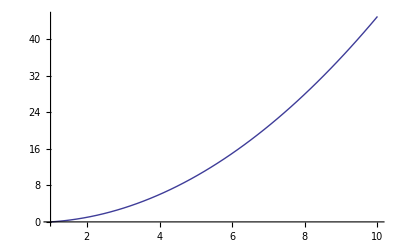

```mathematica
Plot[dimT[1,n],{n,1,10},AxesOrigin->{1,0}]
```

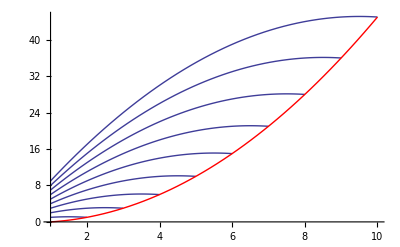

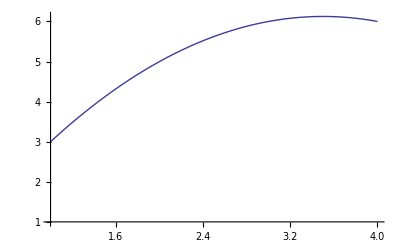

```mathematica
Show[Evaluate[Table[Plot[dimE[m,n],{m,1,n},AxesOrigin->{1,0}],{n,10,2,-1}]],
Plot[dimT[1,n],{n,1,10},PlotStyle->Red]]
```